```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[x1];
s1=Sign[x1-x2];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
G=x1*ae;
u0=x2*ae;
x2=0.1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
T1=Block[{y1=0},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T2=Block[{y1=0.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T3=Block[{y1=1.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T4=Block[{y1=1.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T5=Block[{y1=2.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T6=Block[{y1=2.55},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];


T7=Block[{y1=3.05},P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30];

ca=CoefficientArrays[eqs,vars];

mat=Normal[ca[[2]]];
rhs=-Normal[ca[[1]]];

sol=LinearSolve[mat,rhs];

Abs[sol[[7]]]^2];
list=AppendTo[list1,{x1,Re[T1],Re[T2],Re[T3],Re[T4],Re[T5],Re[T6],Re[T7]}];
},{x1,-1.111,1.111,0.0002}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG2.dat",listn]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«5»,{0.+0. ⅈ,0.+0. ⅈ,-4.93056×10^8-7.13828×10^8 ⅈ,-4.93056×10^8+7.13828×10^8 ⅈ,5.98478×10^27+0. ⅈ,-1.25761×10^-10+0. ⅈ,5.40103×10^8-6.315×10^8 ⅈ,7.50597×10^-10+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-8.23301×10^8 ⅈ,«6»,0.+0. ⅈ},{«1»},«1»,{«1»},{0.+0. ⅈ,«6»,1.09097×10^-9+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-7.10255×10^8-4.85297×10^8 ⅈ,-7.10255×10^8+4.85297×10^8 ⅈ,4.11159×10^27+0. ⅈ,-1.79973×10^-10+0. ⅈ,2.62362×10^8-7.80378×10^8 ⅈ,1.09097×10^-9+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.-8.1564×10^8 ⅈ,«6»,0.+0. ⅈ},{«1»},«1»,{«1»},{0.+0. ⅈ,«6»,1.58523×10^-9+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-8.29846×10^8-1.96916×10^8 ⅈ,-8.29846×10^8+1.96916×10^8 ⅈ,2.8259×10^27+0. ⅈ,-2.57412×10^-10+0. ⅈ,-4.78361×10^7-8.14236×10^8 ⅈ,1.58523×10^-9+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«5»,{0.+0. ⅈ,0.+0. ⅈ,-8.37619×10^8+1.15153×10^8 ⅈ,-8.37619×10^8-1.15153×10^8 ⅈ,1.9358×10^27+0. ⅈ,-3.69288×10^-10+0. ⅈ,-3.48006×10^8-7.29114×10^8 ⅈ,2.31137×10^-9+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«5»,{0.+0. ⅈ,0.+0. ⅈ,-7.31606×10^8+4.08735×10^8 ⅈ,-7.31606×10^8-4.08735×10^8 ⅈ,1.32154×10^27+0. ⅈ,-5.31435×10^-10+0. ⅈ,-5.93487×10^8-5.36594×10^8 ⅈ,3.38214×10^-9+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{75.4161,Null}

TBG2.dat

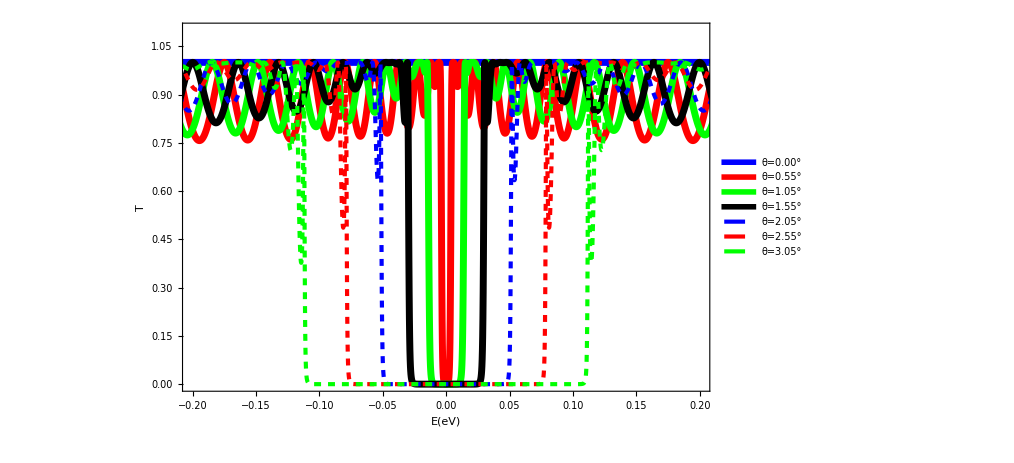

```mathematica
data1=Import["TBG.dat"][[All,{1,2}]];
data2=Import["TBG.dat"][[All,{1,3}]];
data3=Import["TBG.dat"][[All,{1,4}]];
data4=Import["TBG.dat"][[All,{1,5}]];
data5=Import["TBG.dat"][[All,{1,6}]];
data6=Import["TBG.dat"][[All,{1,7}]];
data7=Import["TBG.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6,data7},Frame->True,PlotRange->{{-0.2,0.2},{0,1.1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.55°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E(eV)",25,Black],Rotate[Style["T",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

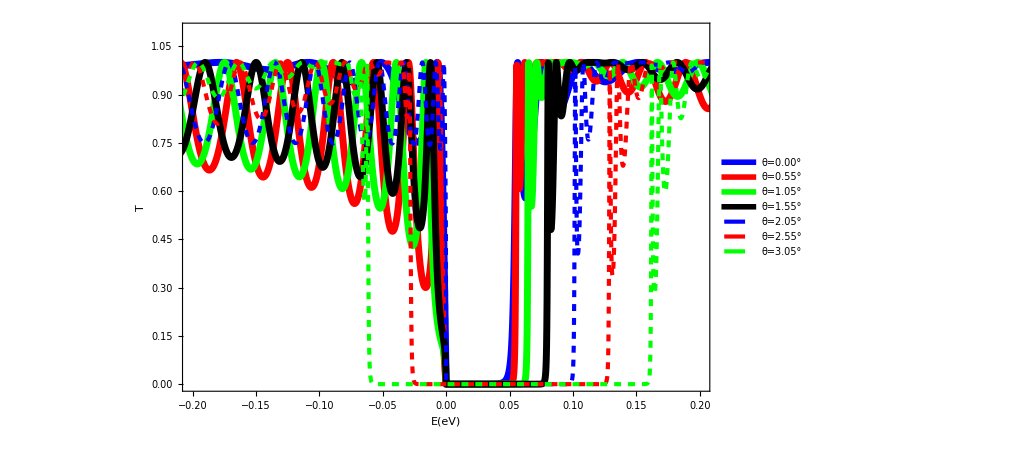

```mathematica
data1=Import["TBG1.dat"][[All,{1,2}]];
data2=Import["TBG1.dat"][[All,{1,3}]];
data3=Import["TBG1.dat"][[All,{1,4}]];
data4=Import["TBG1.dat"][[All,{1,5}]];
data5=Import["TBG1.dat"][[All,{1,6}]];
data6=Import["TBG1.dat"][[All,{1,7}]];
data7=Import["TBG1.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6,data7},Frame->True,PlotRange->{{-0.2,0.2},{0,1.1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.55°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E(eV)",25,Black],Rotate[Style["T",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

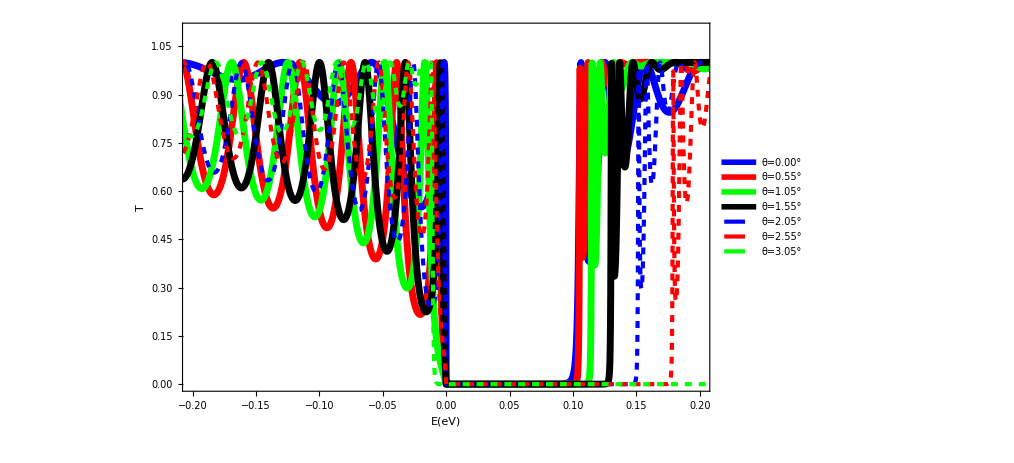

```mathematica
data1=Import["TBG2.dat"][[All,{1,2}]];
data2=Import["TBG2.dat"][[All,{1,3}]];
data3=Import["TBG2.dat"][[All,{1,4}]];
data4=Import["TBG2.dat"][[All,{1,5}]];
data5=Import["TBG2.dat"][[All,{1,6}]];
data6=Import["TBG2.dat"][[All,{1,7}]];
data7=Import["TBG2.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6,data7},Frame->True,PlotRange->{{-0.2,0.2},{0,1.1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.55°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E(eV)",25,Black],Rotate[Style["T",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Calculation of conductance, thermal conductance and Seeback coefficient and figure of merit

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
x2=0.05;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30]//Simplify;

ca=CoefficientArrays[eqs,vars]//Simplify;

mat=Normal[ca[[2]]]//Simplify;
rhs=-Normal[ca[[1]]]//Simplify;

sol=LinearSolve[mat,rhs];

R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran12n.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.0633363+0. ⅈ and 5.96719×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.00453066+0. ⅈ and 1.44412×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000270497+0. ⅈ and 1.55951×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.21834×10^-24}. NIntegrate obtained 3.19191×10^-23+0. ⅈ and 4.80832×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained -9.3211×10^-23+0. ⅈ and 5.09183×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

{3509.59,Null}

TBG_tran12n.dat

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
x2=0.1;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0.00;
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30]//Simplify;

ca=CoefficientArrays[eqs,vars]//Simplify;

mat=Normal[ca[[2]]]//Simplify;
rhs=-Normal[ca[[1]]]//Simplify;

sol=LinearSolve[mat,rhs];

R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran22n.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.106325+0. ⅈ and 8.14192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {2.93396×10^-24}. NIntegrate obtained 0.572563+0. ⅈ and 5.78229×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.00796846+0. ⅈ and 2.2813×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000506547+0. ⅈ and 1.93422×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.21834×10^-24}. NIntegrate obtained 2.64294×10^-23+0. ⅈ and 6.14337×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

{1222.92,Null}

TBG_tran22n.dat

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
x2=0.15;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30]//Simplify;

ca=CoefficientArrays[eqs,vars]//Simplify;

mat=Normal[ca[[2]]]//Simplify;
rhs=-Normal[ca[[1]]]//Simplify;

sol=LinearSolve[mat,rhs];

R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran32n.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.0502438+0. ⅈ and 3.30911×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.00355651+0. ⅈ and 8.48761×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000196807+0. ⅈ and 7.40586×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained -7.73147×10^-23+0. ⅈ and 2.34608×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained -7.05697×10^-25+0. ⅈ and 2.21126×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{1310.64,Null}

TBG_tran32n.dat

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
x2=0.20;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30]//Simplify;

ca=CoefficientArrays[eqs,vars]//Simplify;

mat=Normal[ca[[2]]]//Simplify;
rhs=-Normal[ca[[1]]]//Simplify;

sol=LinearSolve[mat,rhs];

R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran42n.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.00897864+0. ⅈ and 3.60591×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.000610516+0. ⅈ and 1.17169×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.0000299267+0. ⅈ and 1.10259×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained -1.53477×10^-23+0. ⅈ and 2.93421×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained -1.66956×10^-24+0. ⅈ and 2.26374×10^-30 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{1383.21,Null}

TBG_tran42n.dat

```mathematica
Clear["Global`*"]
κx=k √(1+Sin[ϕ]^2);
kx=k*Cos[ϕ];
ky=k*Sin[ϕ];
(*k=√(2m*Abs[G])/hbar;*)
k=√(Abs[G]/γ1);
s=Sign[G];
s1=Sign[G-u0];
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=1/h1;
qx=√(-(ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
λx=√((ky^2+dky^2/4)+√(ky^2 dky^2+((G-u0)/γ)^2));
dkx=0;
dky=(4π)/(3*a0)*2Sin[θ/2];
γ=Piecewise[{{γ1,θ==0},{(2 hbar^2 vf^2)/(15 tu),θ!=0}}];
γ1=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
a=50*10^-9;
a0=0.246*10^-9;
k1p=((qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k1m=((-qx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2p=((I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k2m=((-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx+I*ky)^2-(1/2(dkx+I*dky))^2];
k3p=((-qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k3m=((qx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(qx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4p=((I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
k4m=((-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2)/Abs[(-I*λx-I*ky)^2-(1/2(dkx+I*dky))^2];
(*k2p=1;
k2m=-1;*)
θ=y1*π/180;ϕ=0π/180;
u0=x2*ae;
x2=0.25;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
y1=0;
SetSharedVariable[list1]
list1={};
ParallelDo[{
P11={{Exp[I*kx*x]+r1*Exp[-I*kx*x]+c11*Exp[κx*x]},{s*Exp[I*kx*x+2*I*ϕ]+r1*s*Exp[-I*kx*x-2I*ϕ]-c11*h1*s*Exp[κx*x]}};
P12={{a12*Exp[I*qx*x]+b12*Exp[-I*qx*x]+c12*Exp[λx*x]+d12*Exp[-λx*x]},{a12*s1*k1p*Exp[I*qx*x]+b12*s1*k1m*Exp[-I*qx*x]+c12*s1*k2p*Exp[λx*x]+d12*s1*k2m*Exp[-λx*x]}};
P13={{t1*Exp[I*kx*x]+d13*Exp[-κx*x]},{t1*s*Exp[I*kx*x+2*I*ϕ]-d13/h1*s*Exp[-κx*x]}};
A11=Part[P11,1,1];
A12=Part[P11,2,1];
B11=Part[P12,1,1];
B12=Part[P12,2,1];
C11=Part[P13,1,1];
C12=Part[P13,2,1];
S11=A11-B11/.{x->0};
S12=A12-B12/.{x->0};
S13=D[A11-B11,x]/.{x->0};
S14=D[A12-B12,x]/.{x->0};
S15=B11-C11/.{x->a};
S16=B12-C12/.{x->a};
S17=D[B11-C11,x]/.{x->a};
S18=D[B12-C12,x]/.{x->a};
vars={r1,c11,a12,b12,c12,d12,t1,d13};

eqs=N[{S11,S12,S13,S14,S15,S16,S17,S18},30]//Simplify;

ca=CoefficientArrays[eqs,vars]//Simplify;

mat=Normal[ca[[2]]]//Simplify;
rhs=-Normal[ca[[1]]]//Simplify;

sol=LinearSolve[mat,rhs];

R1=Abs[sol[[7]]]^2;
Cond=NIntegrate[R1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[R1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[R1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran52n.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.00696225+0. ⅈ and 4.7056×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.000489736+0. ⅈ and 1.51968×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000026698+0. ⅈ and 1.46619×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained -1.08348×10^-23+0. ⅈ and 3.4793×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained -9.50259×10^-26+0. ⅈ and 4.26453×10^-31 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{1344.82,Null}

TBG_tran52n.dat

# L=50nm results

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

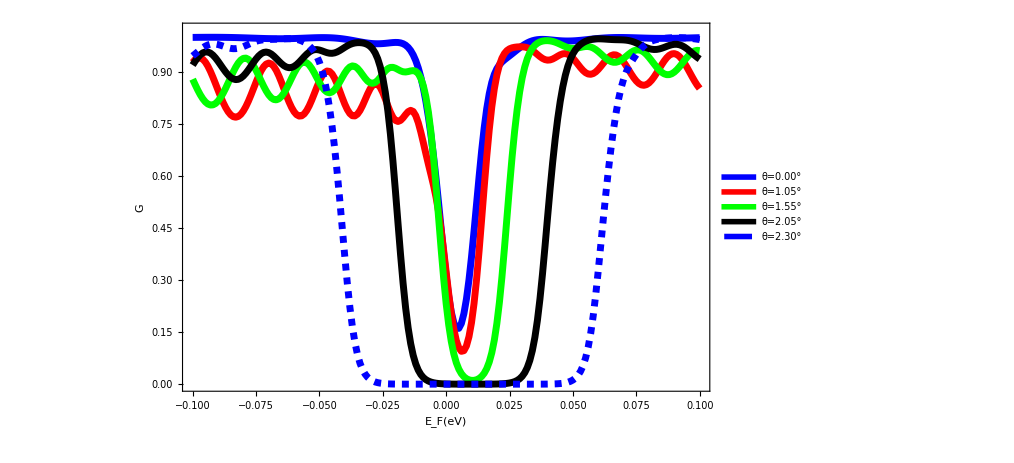

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,2}]];
data2=Import["TBG_tran22.dat"][[All,{1,2}]];
data3=Import["TBG_tran32.dat"][[All,{1,2}]];
data4=Import["TBG_tran42.dat"][[All,{1,2}]];
data5=Import["TBG_tran52.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->{{-0.1,0.1},{0,1.02}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["G",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

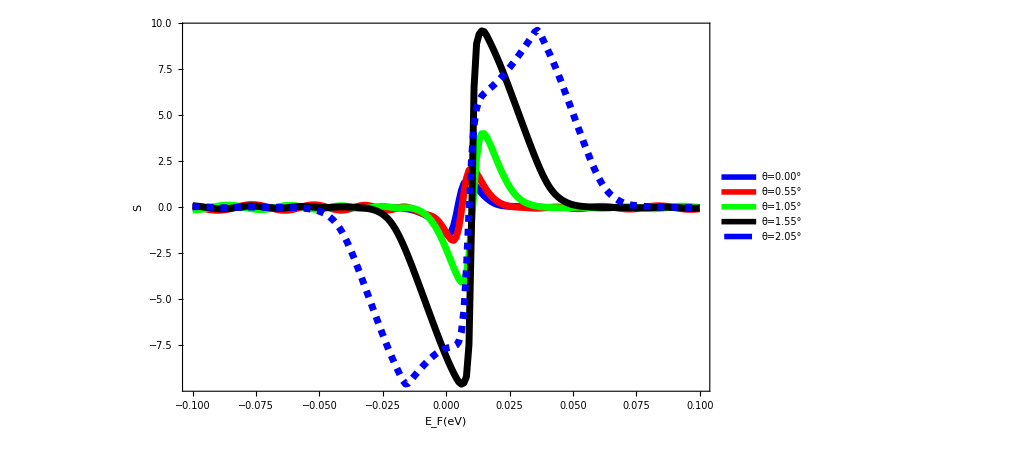

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,3}]];
data2=Import["TBG_tran22.dat"][[All,{1,3}]];
data3=Import["TBG_tran32.dat"][[All,{1,3}]];
data4=Import["TBG_tran42.dat"][[All,{1,3}]];
data5=Import["TBG_tran52.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["S",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

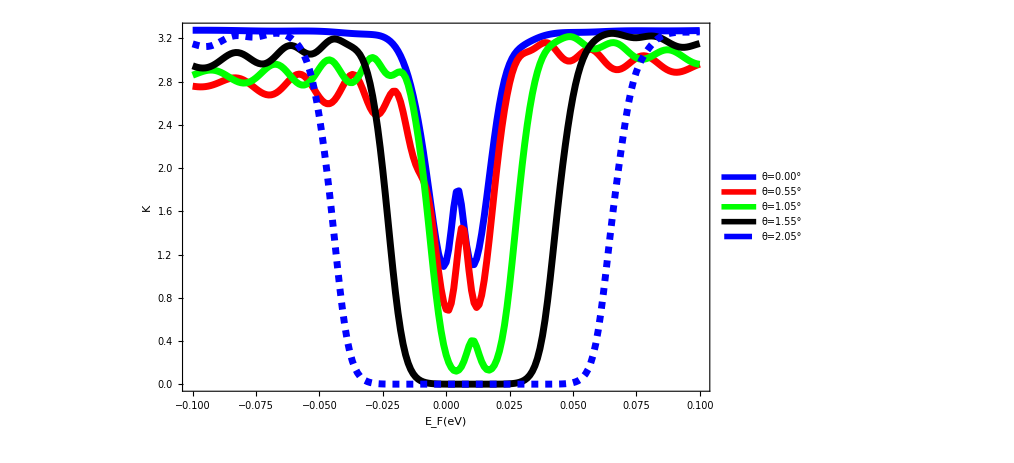

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,4}]];
data2=Import["TBG_tran22.dat"][[All,{1,4}]];
data3=Import["TBG_tran32.dat"][[All,{1,4}]];
data4=Import["TBG_tran42.dat"][[All,{1,4}]];
data5=Import["TBG_tran52.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["K",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

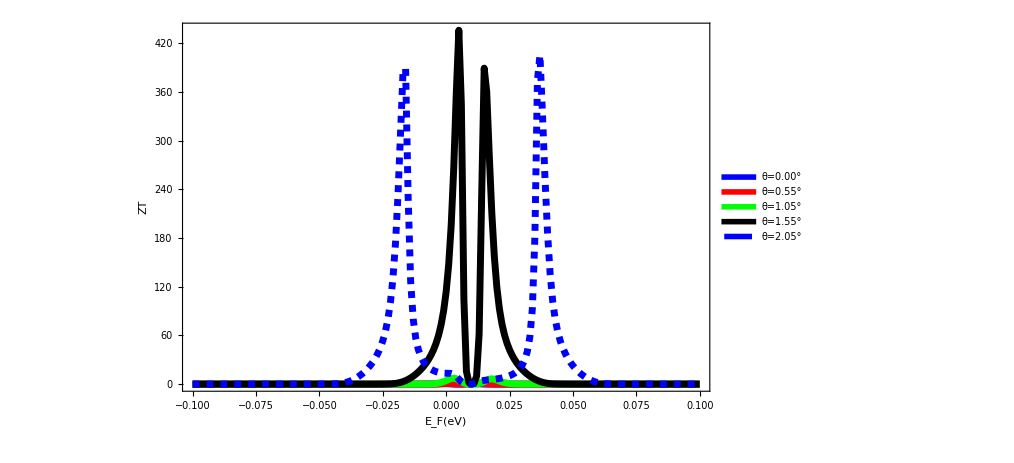

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,5}]];
data2=Import["TBG_tran22.dat"][[All,{1,5}]];
data3=Import["TBG_tran32.dat"][[All,{1,5}]];
data4=Import["TBG_tran42.dat"][[All,{1,5}]];
data5=Import["TBG_tran52.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["ZT",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

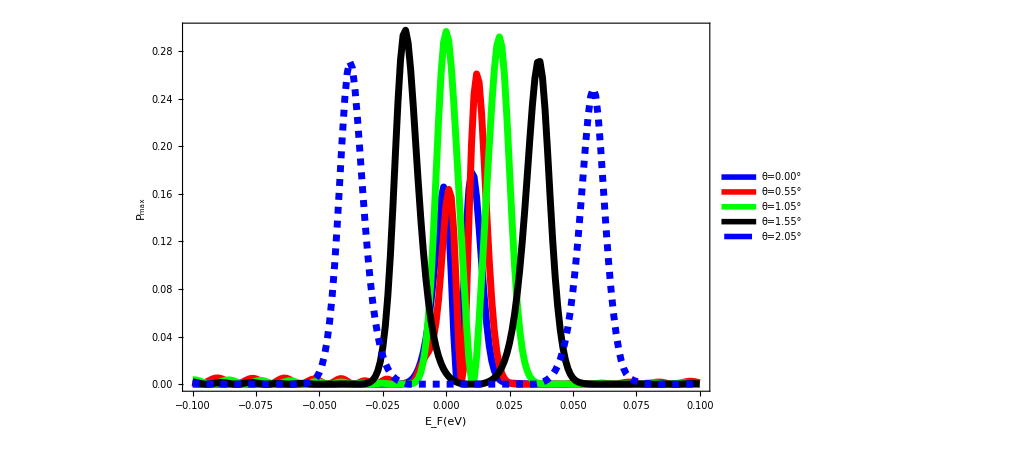

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,6}]];
data2=Import["TBG_tran22.dat"][[All,{1,6}]];
data3=Import["TBG_tran32.dat"][[All,{1,6}]];
data4=Import["TBG_tran42.dat"][[All,{1,6}]];
data5=Import["TBG_tran52.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["P_max",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

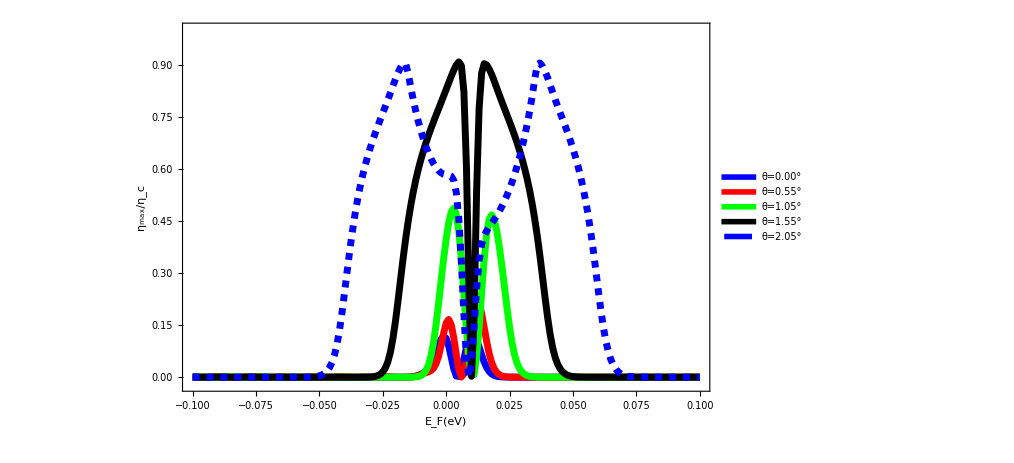

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,7}]];
data2=Import["TBG_tran22.dat"][[All,{1,7}]];
data3=Import["TBG_tran32.dat"][[All,{1,7}]];
data4=Import["TBG_tran42.dat"][[All,{1,7}]];
data5=Import["TBG_tran52.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->{{-0.1,0.1},{-0.02,1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

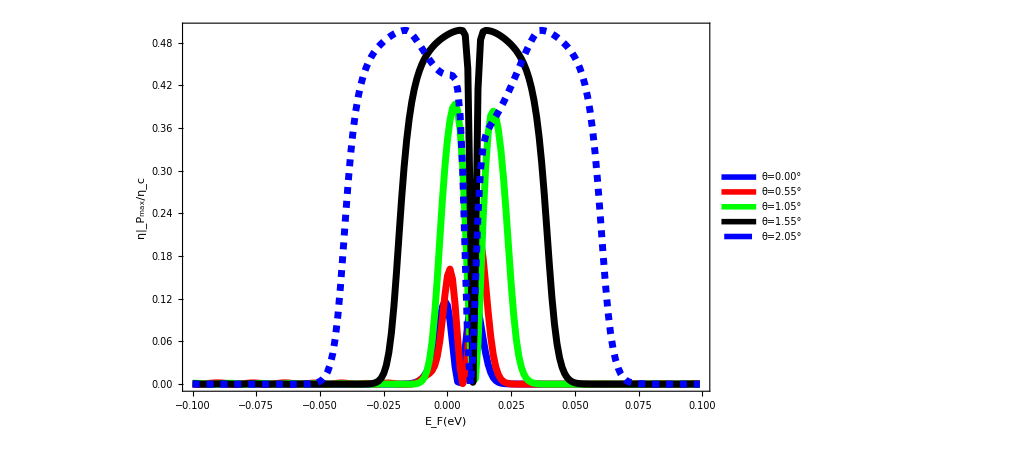

```mathematica
data1=Table[Flatten[{Import["TBG_tran12.dat"][[x]][[1]],Import["TBG_tran12.dat"][[x]][[5]]/(2Import["TBG_tran12.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data2=Table[Flatten[{Import["TBG_tran22.dat"][[x]][[1]],Import["TBG_tran22.dat"][[x]][[5]]/(2Import["TBG_tran22.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data3=Table[Flatten[{Import["TBG_tran32.dat"][[x]][[1]],Import["TBG_tran32.dat"][[x]][[5]]/(2Import["TBG_tran32.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data4=Table[Flatten[{Import["TBG_tran42.dat"][[x]][[1]],Import["TBG_tran42.dat"][[x]][[5]]/(2Import["TBG_tran42.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data5=Table[Flatten[{Import["TBG_tran52.dat"][[x]][[1]],Import["TBG_tran52.dat"][[x]][[5]]/(2Import["TBG_tran52.dat"][[x]][[5]]+4)}],{x,1,200,1}];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η|_P_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

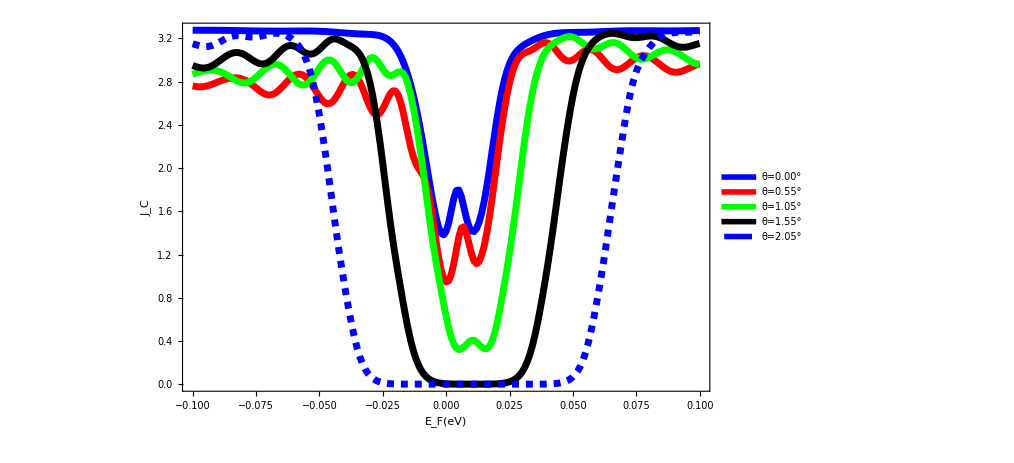

```mathematica
data1=Import["TBG_tran12.dat"][[All,{1,8}]];
data2=Import["TBG_tran22.dat"][[All,{1,8}]];
data3=Import["TBG_tran32.dat"][[All,{1,8}]];
data4=Import["TBG_tran42.dat"][[All,{1,8}]];
data5=Import["TBG_tran52.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["J_C",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# L=50nm results

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

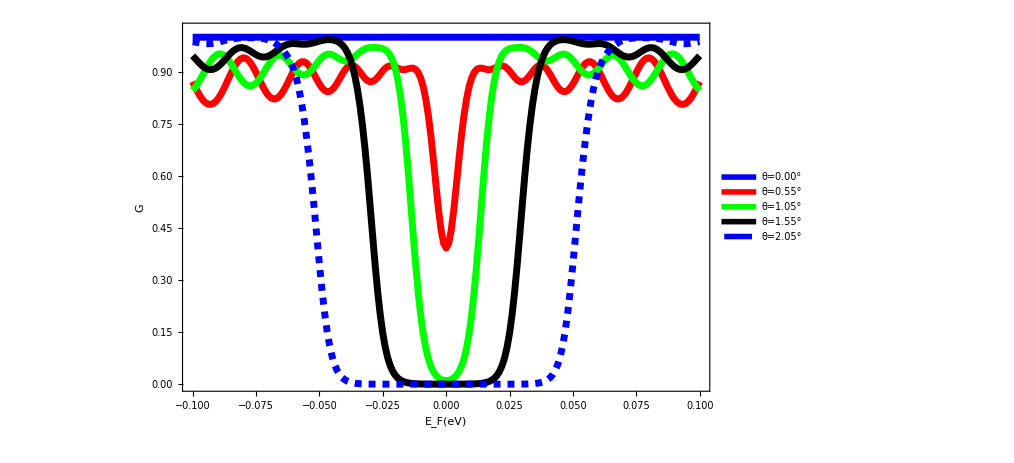

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,2}]];
data2=Import["TBG_tran22s.dat"][[All,{1,2}]];
data3=Import["TBG_tran32s.dat"][[All,{1,2}]];
data4=Import["TBG_tran42s.dat"][[All,{1,2}]];
data5=Import["TBG_tran52s.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->{{-0.1,0.1},{0,1.02}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["G",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

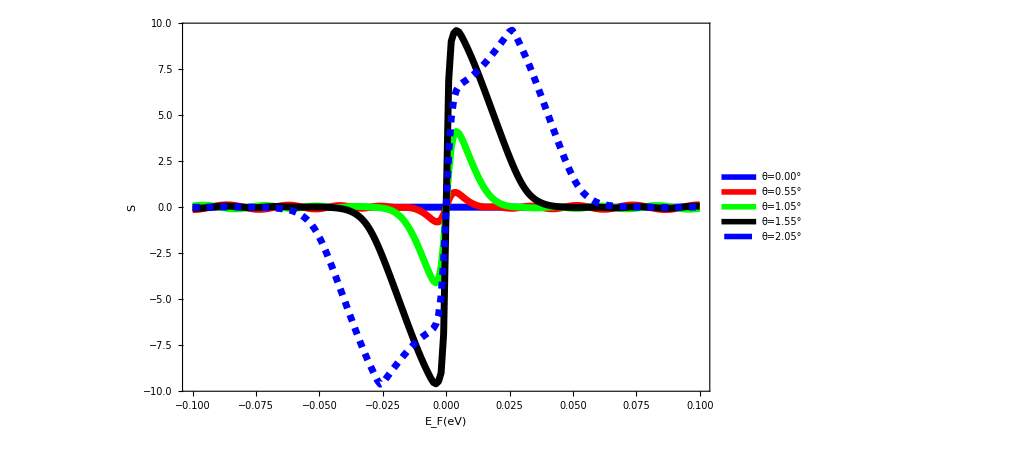

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,3}]];
data2=Import["TBG_tran22s.dat"][[All,{1,3}]];
data3=Import["TBG_tran32s.dat"][[All,{1,3}]];
data4=Import["TBG_tran42s.dat"][[All,{1,3}]];
data5=Import["TBG_tran52s.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["S",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

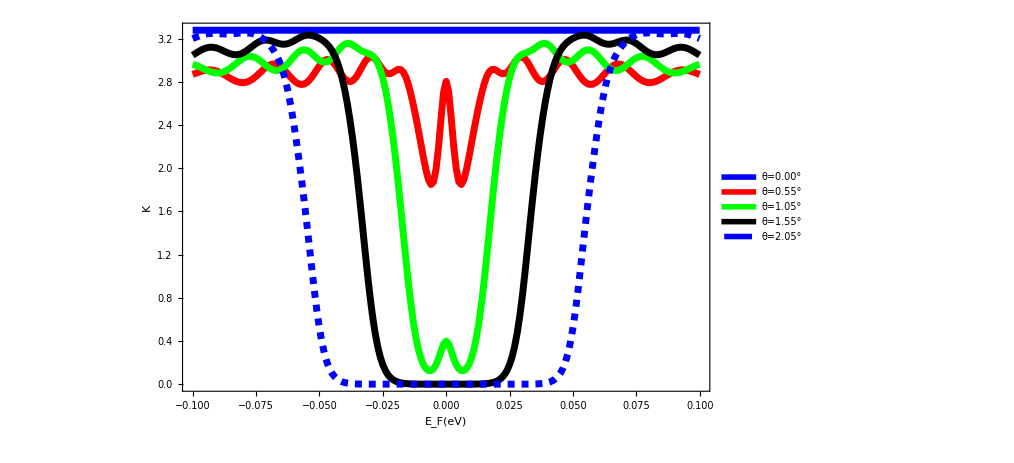

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,4}]];
data2=Import["TBG_tran22s.dat"][[All,{1,4}]];
data3=Import["TBG_tran32s.dat"][[All,{1,4}]];
data4=Import["TBG_tran42s.dat"][[All,{1,4}]];
data5=Import["TBG_tran52s.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["K",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

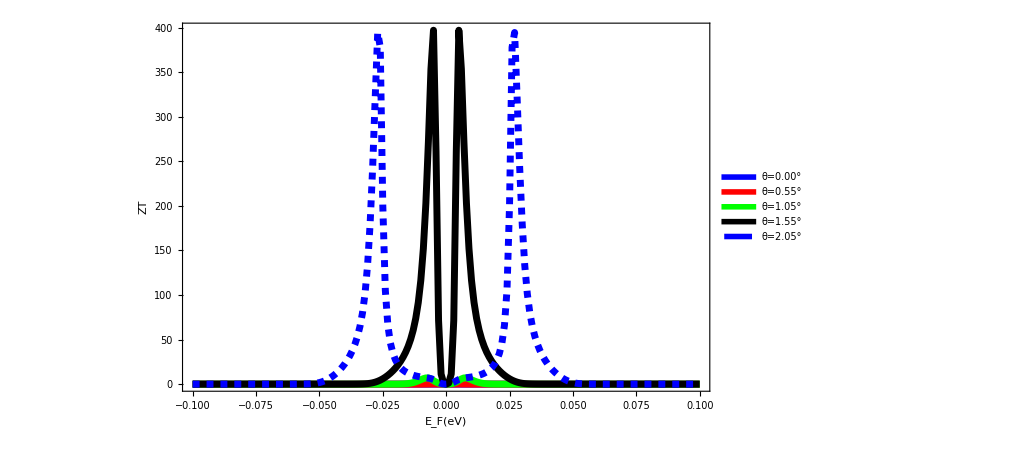

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,5}]];
data2=Import["TBG_tran22s.dat"][[All,{1,5}]];
data3=Import["TBG_tran32s.dat"][[All,{1,5}]];
data4=Import["TBG_tran42s.dat"][[All,{1,5}]];
data5=Import["TBG_tran52s.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["ZT",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

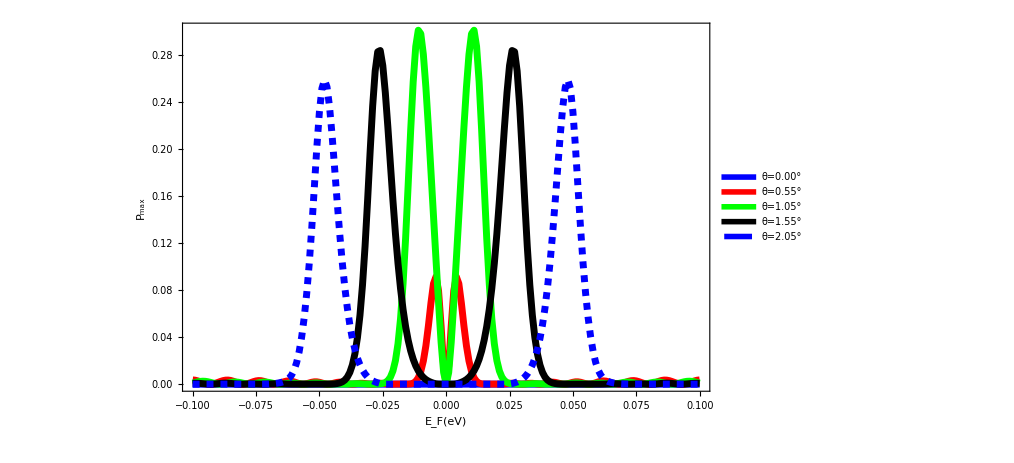

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,6}]];
data2=Import["TBG_tran22s.dat"][[All,{1,6}]];
data3=Import["TBG_tran32s.dat"][[All,{1,6}]];
data4=Import["TBG_tran42s.dat"][[All,{1,6}]];
data5=Import["TBG_tran52s.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["P_max",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

```mathematica
data5
```

{{-0.1,4.82442×10^-7},{-0.099,1.99204×10^-6},{-0.098,2.98408×10^-6},{-0.097,2.72194×10^-6},{-0.096,1.49906×10^-6},{-0.095,2.7936×10^-7},{-0.094,1.14638×10^-7},{-0.093,1.60907×10^-6},{-0.092,4.64708×10^-6},{-0.091,8.46484×10^-6},{-0.09,0.0000119916},{-0.089,0.0000142817},{-0.088,0.000014844},{-0.087,0.0000137454},{-0.086,0.0000114855},{-0.085,8.73761×10^-6},{-0.084,6.0929×10^-6},{-0.083,3.90868×10^-6},{-0.082,2.29555×10^-6},{-0.081,1.2018×10^-6},{-0.08,5.15175×10^-7},{-0.079,1.33365×10^-7},{-0.078,4.15973×10^-10},{-0.077,1.21813×10^-7},{-0.076,6.65598×10^-7},{-0.075,1.9734×10^-6},{-0.074,4.61669×10^-6},{-0.073,9.54957×10^-6},{-0.072,0.000018293},{-0.071,0.0000331473},{-0.07,0.0000573675},{-0.069,0.0000952311},{-0.068,0.000152055},{-0.067,0.000234561},{-0.066,0.000352502},{-0.065,0.000522938},{-0.064,0.000778807},{-0.063,0.00118363},{-0.062,0.00185406},{-0.061,0.00298995},{-0.06,0.00490509},{-0.059,0.00804496},{-0.058,0.012985},{-0.057,0.0204407},{-0.056,0.0313558},{-0.055,0.0470885},{-0.054,0.0695316},{-0.053,0.100806},{-0.052,0.142261},{-0.051,0.193207},{-0.05,0.250543},{-0.049,0.309884},{-0.048,0.36728},{-0.047,0.420232},{-0.046,0.467714},{-0.045,0.509721},{-0.044,0.546771},{-0.043,0.579579},{-0.042,0.608874},{-0.041,0.635323},{-0.04,0.659503},{-0.039,0.681906},{-0.038,0.702944},{-0.037,0.722974},{-0.036,0.742329},{-0.035,0.761358},{-0.034,0.78045},{-0.033,0.80002},{-0.032,0.820353},{-0.031,0.841218},{-0.03,0.861516},{-0.029,0.879668},{-0.028,0.894386},{-0.027,0.904247},{-0.026,0.902277},{-0.025,0.868503},{-0.024,0.823318},{-0.023,0.782438},{-0.022,0.745891},{-0.021,0.712883},{-0.02,0.682899},{-0.019,0.655602},{-0.018,0.630748},{-0.017,0.608144},{-0.016,0.58763},{-0.015,0.569065},{-0.014,0.552329},{-0.013,0.537313},{-0.012,0.523919},{-0.011,0.512041},{-0.01,0.501527},{-0.009,0.492076},{-0.008,0.483},{-0.007,0.472608},{-0.006,0.456986},{-0.005,0.427599},{-0.004,0.37097},{-0.003,0.275921},{-0.002,0.153057},{-0.001,0.0440531},{-1.73472×10^-18,0.},{0.001,0.0440531},{0.002,0.153057},{0.003,0.275921},{0.004,0.37097},{0.005,0.427599},{0.006,0.456986},{0.007,0.472608},{0.008,0.483},{0.009,0.492076},{0.01,0.501527},{0.011,0.512041},{0.012,0.523919},{0.013,0.537313},{0.014,0.552329},{0.015,0.569065},{0.016,0.58763},{0.017,0.608144},{0.018,0.630748},{0.019,0.655602},{0.02,0.682899},{0.021,0.712883},{0.022,0.745891},{0.023,0.782438},{0.024,0.823318},{0.025,0.868503},{0.026,0.902277},{0.027,0.904247},{0.028,0.894386},{0.029,0.879668},{0.03,0.861516},{0.031,0.841218},{0.032,0.820353},{0.033,0.80002},{0.034,0.78045},{0.035,0.761358},{0.036,0.742329},{0.037,0.722974},{0.038,0.702944},{0.039,0.681906},{0.04,0.659503},{0.041,0.635323},{0.042,0.608874},{0.043,0.579579},{0.044,0.546771},{0.045,0.509721},{0.046,0.467714},{0.047,0.420232},{0.048,0.36728},{0.049,0.309884},{0.05,0.250543},{0.051,0.193207},{0.052,0.142261},{0.053,0.100806},{0.054,0.0695316},{0.055,0.0470885},{0.056,0.0313558},{0.057,0.0204407},{0.058,0.012985},{0.059,0.00804496},{0.06,0.00490509},{0.061,0.00298995},{0.062,0.00185406},{0.063,0.00118363},{0.064,0.000778807},{0.065,0.000522938},{0.066,0.000352502},{0.067,0.000234561},{0.068,0.000152055},{0.069,0.0000952311},{0.07,0.0000573675},{0.071,0.0000331473},{0.072,0.000018293},{0.073,9.54957×10^-6},{0.074,4.61669×10^-6},{0.075,1.9734×10^-6},{0.076,6.65598×10^-7},{0.077,1.21813×10^-7},{0.078,4.15973×10^-10},{0.079,1.33365×10^-7},{0.08,5.15175×10^-7},{0.081,1.2018×10^-6},{0.082,2.29555×10^-6},{0.083,3.90868×10^-6},{0.084,6.0929×10^-6},{0.085,8.73761×10^-6},{0.086,0.0000114855},{0.087,0.0000137454},{0.088,0.000014844},{0.089,0.0000142817},{0.09,0.0000119916},{0.091,8.46484×10^-6},{0.092,4.64708×10^-6},{0.093,1.60907×10^-6},{0.094,1.14638×10^-7},{0.095,2.7936×10^-7},{0.096,1.49906×10^-6},{0.097,2.72194×10^-6},{0.098,2.98408×10^-6},{0.099,1.99204×10^-6},{0.1,4.82442×10^-7}}

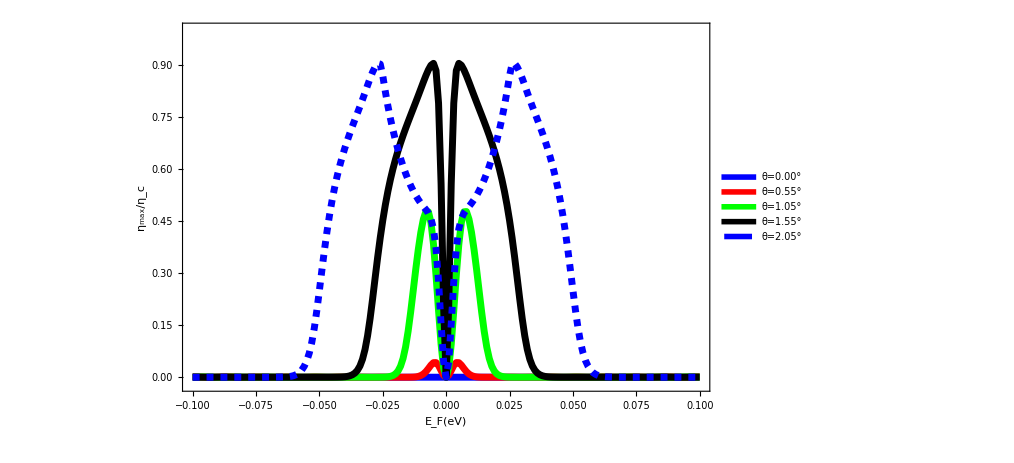

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,7}]];
data2=Import["TBG_tran22s.dat"][[All,{1,7}]];
data3=Import["TBG_tran32s.dat"][[All,{1,7}]];
data4=Import["TBG_tran42s.dat"][[All,{1,7}]];
data5=Import["TBG_tran52s.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->{{-0.1,0.1},{-0.02,1}},ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

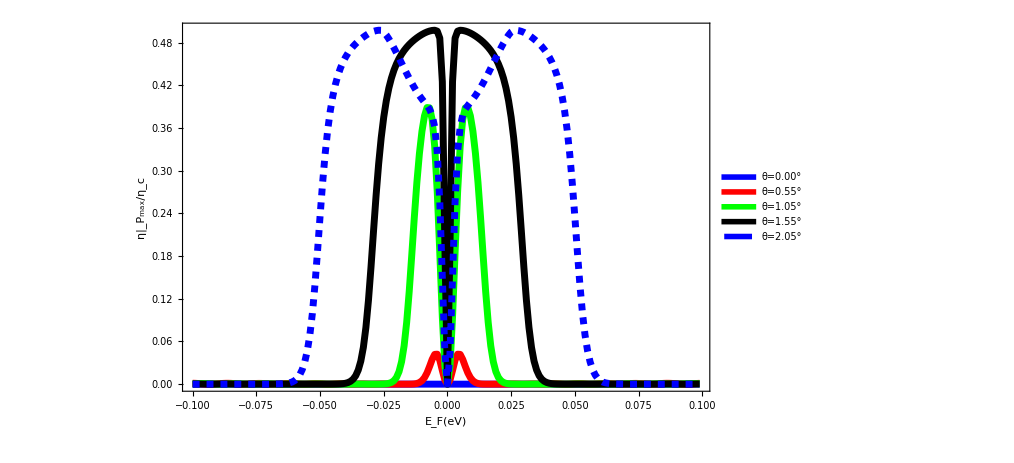

```mathematica
data1=Table[Flatten[{Import["TBG_tran12s.dat"][[x]][[1]],Import["TBG_tran12s.dat"][[x]][[5]]/(2Import["TBG_tran12s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data2=Table[Flatten[{Import["TBG_tran22s.dat"][[x]][[1]],Import["TBG_tran22s.dat"][[x]][[5]]/(2Import["TBG_tran22s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data3=Table[Flatten[{Import["TBG_tran32s.dat"][[x]][[1]],Import["TBG_tran32s.dat"][[x]][[5]]/(2Import["TBG_tran32s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data4=Table[Flatten[{Import["TBG_tran42s.dat"][[x]][[1]],Import["TBG_tran42s.dat"][[x]][[5]]/(2Import["TBG_tran42s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data5=Table[Flatten[{Import["TBG_tran52s.dat"][[x]][[1]],Import["TBG_tran52s.dat"][[x]][[5]]/(2Import["TBG_tran52s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η|_P_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

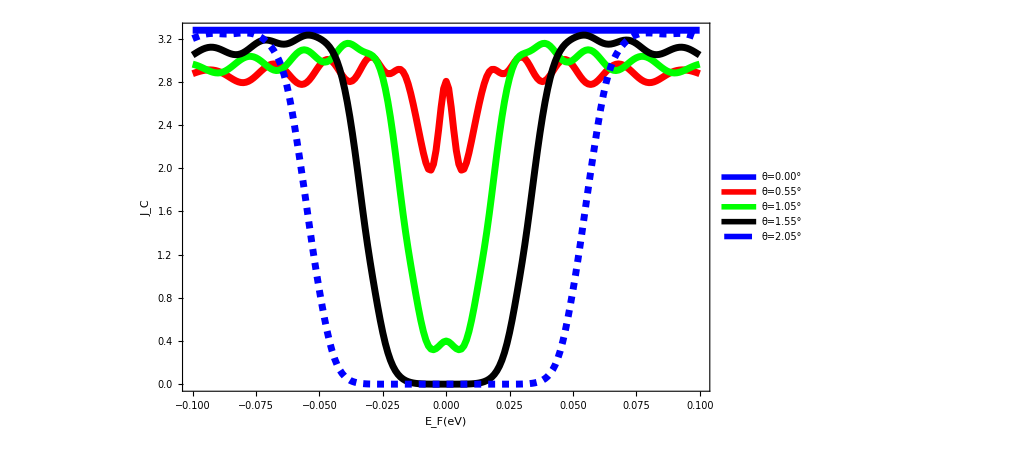

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,8}]];
data2=Import["TBG_tran22s.dat"][[All,{1,8}]];
data3=Import["TBG_tran32s.dat"][[All,{1,8}]];
data4=Import["TBG_tran42s.dat"][[All,{1,8}]];
data5=Import["TBG_tran52s.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"θ=0.00°","θ=0.55°","θ=1.05°","θ=1.55°","θ=2.05°","θ=2.30°","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["J_C",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# L=50nm results

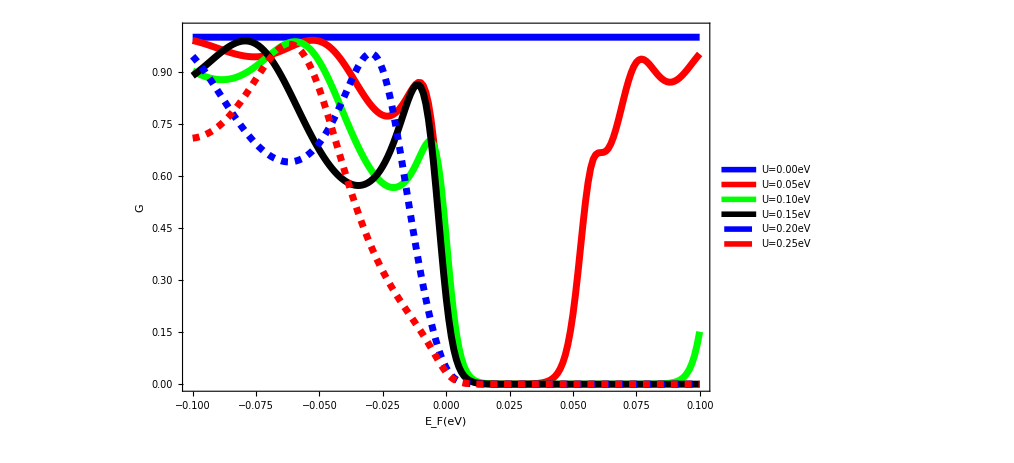

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,2}]];
data2=Import["TBG_tran12n.dat"][[All,{1,2}]];
data3=Import["TBG_tran22n.dat"][[All,{1,2}]];
data4=Import["TBG_tran32n.dat"][[All,{1,2}]];
data5=Import["TBG_tran42n.dat"][[All,{1,2}]];
data6=Import["TBG_tran52n.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->{{-0.1,0.1},{0,1.02}},ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["G",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

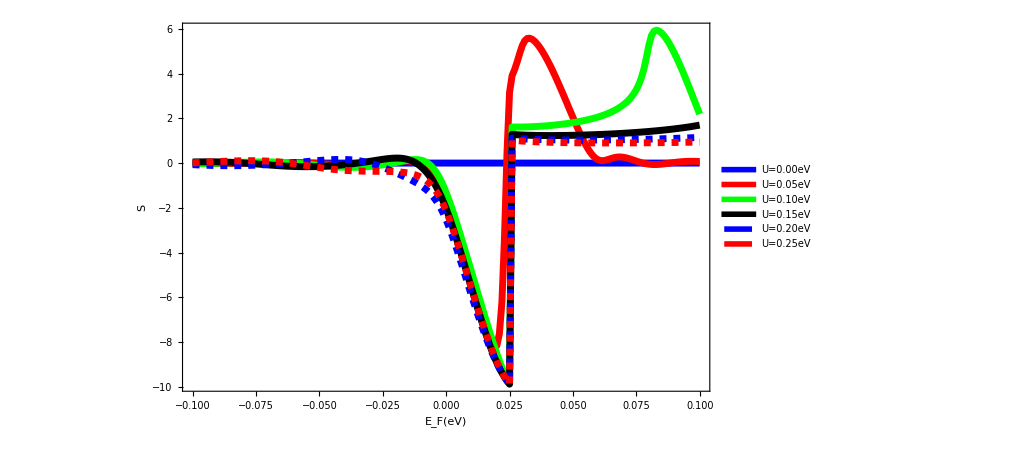

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,3}]];
data2=Import["TBG_tran12n.dat"][[All,{1,3}]];
data3=Import["TBG_tran22n.dat"][[All,{1,3}]];
data4=Import["TBG_tran32n.dat"][[All,{1,3}]];
data5=Import["TBG_tran42n.dat"][[All,{1,3}]];
data6=Import["TBG_tran52n.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["S",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

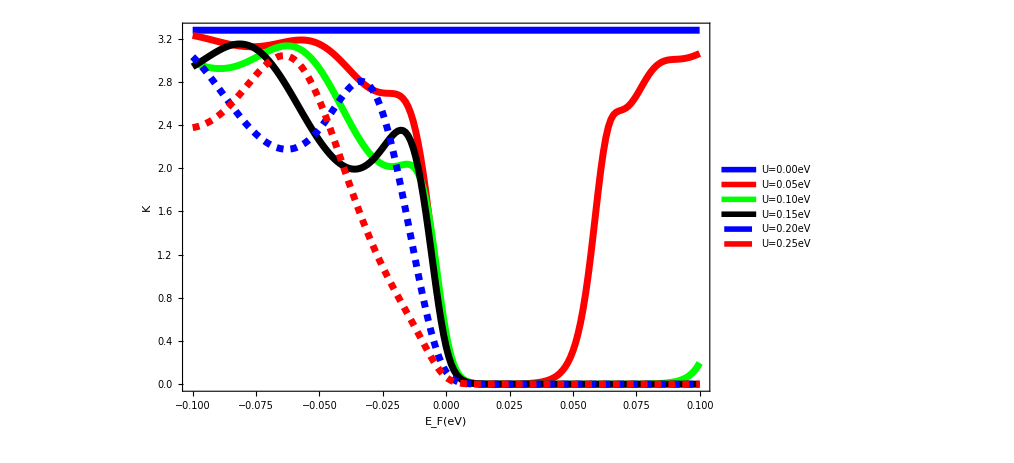

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,4}]];
data2=Import["TBG_tran12n.dat"][[All,{1,4}]];
data3=Import["TBG_tran22n.dat"][[All,{1,4}]];
data4=Import["TBG_tran32n.dat"][[All,{1,4}]];
data5=Import["TBG_tran42n.dat"][[All,{1,4}]];
data6=Import["TBG_tran52n.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["K",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

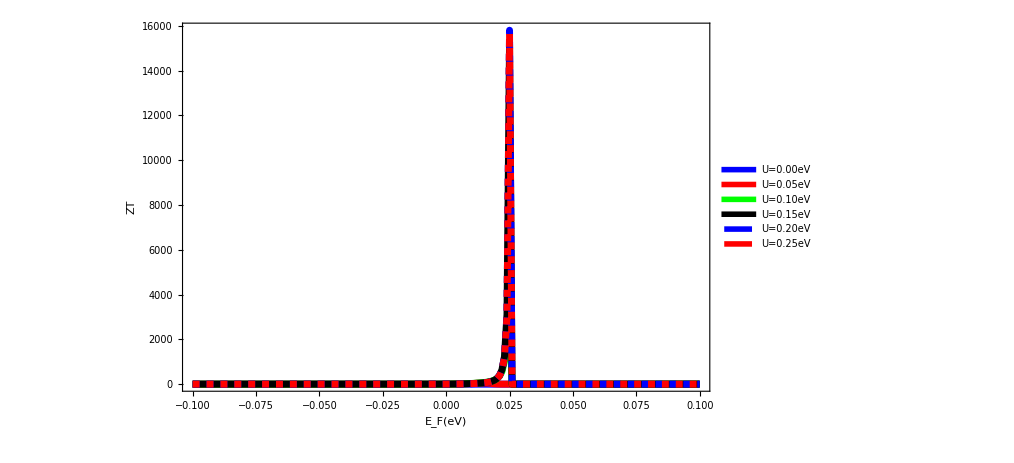

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,5}]];
data2=Import["TBG_tran12n.dat"][[All,{1,5}]];
data3=Import["TBG_tran22n.dat"][[All,{1,5}]];
data4=Import["TBG_tran32n.dat"][[All,{1,5}]];
data5=Import["TBG_tran42n.dat"][[All,{1,5}]];
data6=Import["TBG_tran52n.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["ZT",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

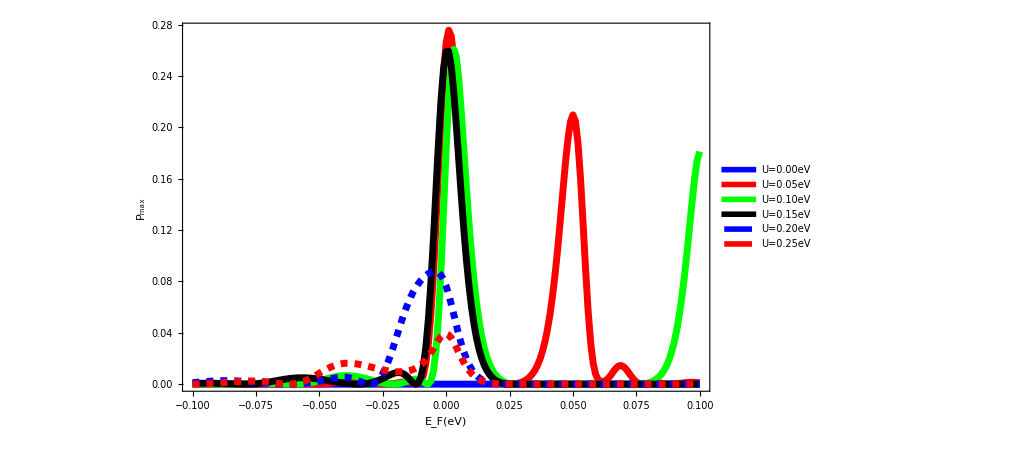

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,6}]];
data2=Import["TBG_tran12n.dat"][[All,{1,6}]];
data3=Import["TBG_tran22n.dat"][[All,{1,6}]];
data4=Import["TBG_tran32n.dat"][[All,{1,6}]];
data5=Import["TBG_tran42n.dat"][[All,{1,6}]];
data6=Import["TBG_tran52n.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["P_max",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

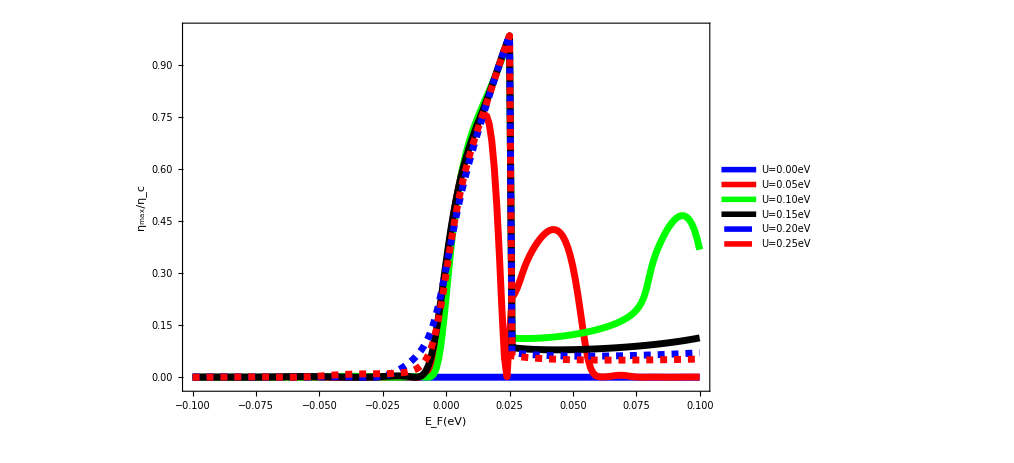

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,7}]];
data2=Import["TBG_tran12n.dat"][[All,{1,7}]];
data3=Import["TBG_tran22n.dat"][[All,{1,7}]];
data4=Import["TBG_tran32n.dat"][[All,{1,7}]];
data5=Import["TBG_tran42n.dat"][[All,{1,7}]];
data6=Import["TBG_tran52n.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->{{-0.1,0.1},{-0.02,1}},ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

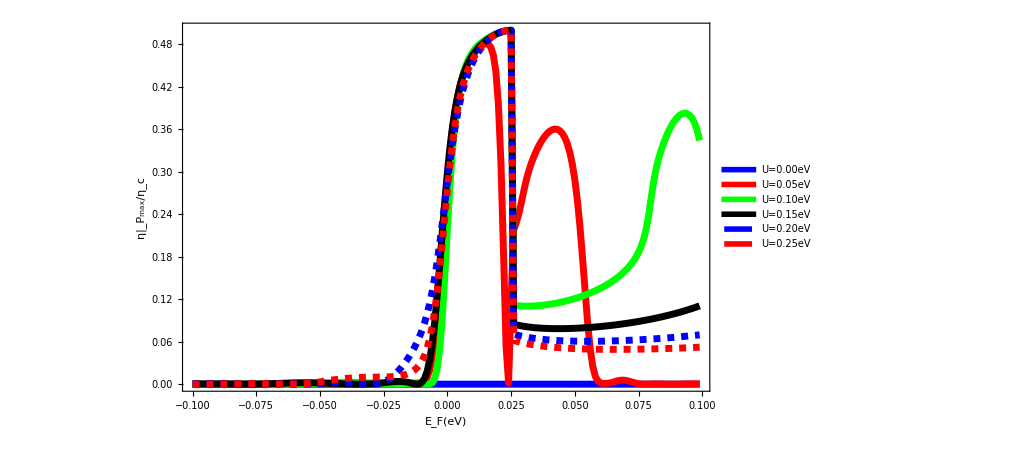

```mathematica
data1=Table[Flatten[{Import["TBG_tran12s.dat"][[x]][[1]],Import["TBG_tran12s.dat"][[x]][[5]]/(2Import["TBG_tran12s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data2=Table[Flatten[{Import["TBG_tran12n.dat"][[x]][[1]],Import["TBG_tran12n.dat"][[x]][[5]]/(2Import["TBG_tran12n.dat"][[x]][[5]]+4)}],{x,1,200,1}];data3=Table[Flatten[{Import["TBG_tran22n.dat"][[x]][[1]],Import["TBG_tran22n.dat"][[x]][[5]]/(2Import["TBG_tran22n.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data4=Table[Flatten[{Import["TBG_tran32n.dat"][[x]][[1]],Import["TBG_tran32n.dat"][[x]][[5]]/(2Import["TBG_tran32n.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data5=Table[Flatten[{Import["TBG_tran42n.dat"][[x]][[1]],Import["TBG_tran42n.dat"][[x]][[5]]/(2Import["TBG_tran42n.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data6=Table[Flatten[{Import["TBG_tran52n.dat"][[x]][[1]],Import["TBG_tran52n.dat"][[x]][[5]]/(2Import["TBG_tran52n.dat"][[x]][[5]]+4)}],{x,1,200,1}];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η|_P_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

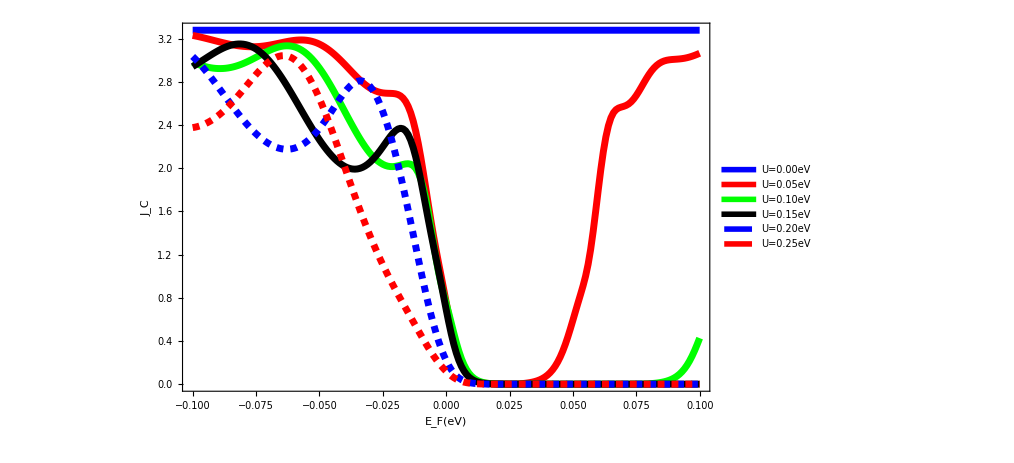

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,8}]];
data2=Import["TBG_tran12n.dat"][[All,{1,8}]];
data3=Import["TBG_tran22n.dat"][[All,{1,8}]];
data4=Import["TBG_tran32n.dat"][[All,{1,8}]];
data5=Import["TBG_tran42n.dat"][[All,{1,8}]];
data6=Import["TBG_tran52n.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3,data4,data5,data6},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV","U=0.15eV","U=0.20eV","U=0.25eV","θ=3.05°"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["J_C",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Calculation of conductance, thermal conductance and Seeback coefficient and figure of merit in bilayer graphene-strained bilayer graphene-bilayer graphene

# Electron incident

```mathematica
Clear["Global`*"]
P1={{Exp[I*kx*x]+r*Exp[-I*kx*x]+c1*Exp[κx*x]},{s*Exp[I*kx*x+2I*ϕ]+s*r*Exp[-I*kx*x-2I*ϕ]-s*c1*h1*Exp[κx*x]}};
P2={{a2*Exp[I*qx*x]+b2*Exp[-I*qx*x]+c2*Exp[λx*x]+d2*Exp[-λx*x]},{a2*s1*Exp[I*qx*x+2I*θ]+s1*b2*Exp[-I*qx*x-2I*θ]-c2*s1*h2*Exp[λx*x]-d2*s1/h2*Exp[-λx*x]}};
P3={{t*Exp[I*kx*x]+d3*Exp[-κx*x]},{t*s*Exp[I*kx*x+2I*ϕ]-d3*s/h1*Exp[-κx*x]}};
A1=Part[P1,1,1];
A2=Part[P1,2,1];
B1=Part[P2,1,1];
B2=Part[P2,2,1];
C1=Part[P3,1,1];
C2=Part[P3,2,1];
ϕ=θ=0;
κx=kx √(1+Sin[ϕ]^2);
λx=qx √(1+Sin[θ]^2);
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=(√(1+Sin[θ]^2)-Sin[θ])^2;
S1=A1-B1/.{x->0};
S2=A2-B2/.{x->0};
S3=D[A1-B1,x]/.{x->0};
S4=D[A2-B2,x]/.{x->0};
S5=B1-C1/.{x->a};
S6=B2-C2/.{x->a};
S7=D[B1-C1,x]/.{x->a};
S8=D[B2-C2,x]/.{x->a};
P=Solve[{S1==0,S2==0,S3==0,S4==0,S5==0,S6==0,S7==0,S8==0},{r,c1,a2,b2,c2,d2,t,d3}]//Simplify;
t=t/.P[[1]]
r=r/.P[[1]]
```

(4 ⅇ^(-ⅈ a kx) kx qx s s1 (ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2-ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2+ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2-ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4))

(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4))

# Hole incident

```mathematica
Clear["Global`*"]
P1={{Exp[-I*kx*x]+r*Exp[I*kx*x]+c1*Exp[κx*x]},{s*Exp[-I*kx*x-2I*ϕ]+s*r*Exp[I*kx*x+2I*ϕ]-s*c1*h1*Exp[κx*x]}};
P2={{a2*Exp[-I*qx*x]+b2*Exp[I*qx*x]+c2*Exp[λx*x]+d2*Exp[-λx*x]},{a2*s1*Exp[-I*qx*x-2I*θ]+s1*b2*Exp[I*qx*x+2I*θ]-c2*s1*h2*Exp[λx*x]-d2*s1/h2*Exp[-λx*x]}};
P3={{t*Exp[-I*kx*x]+d3*Exp[-κx*x]},{t*s*Exp[-I*kx*x-2I*ϕ]-d3*s/h1*Exp[-κx*x]}};
A1=Part[P1,1,1];
A2=Part[P1,2,1];
B1=Part[P2,1,1];
B2=Part[P2,2,1];
C1=Part[P3,1,1];
C2=Part[P3,2,1];
ϕ=θ=0;
κx=kx √(1+Sin[ϕ]^2);
λx=qx √(1+Sin[θ]^2);
h1=(√(1+Sin[ϕ]^2)-Sin[ϕ])^2;
h2=(√(1+Sin[θ]^2)-Sin[θ])^2;
S1=A1-B1/.{x->0};
S2=A2-B2/.{x->0};
S3=D[A1-B1,x]/.{x->0};
S4=D[A2-B2,x]/.{x->0};
S5=B1-C1/.{x->a};
S6=B2-C2/.{x->a};
S7=D[B1-C1,x]/.{x->a};
S8=D[B2-C2,x]/.{x->a};
P=Solve[{S1==0,S2==0,S3==0,S4==0,S5==0,S6==0,S7==0,S8==0},{r,c1,a2,b2,c2,d2,t,d3}]//Simplify;
t=t/.P[[1]]
r=r/.P[[1]]
```

(4 ⅇ^(ⅈ a kx) kx qx s s1 (-ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2+ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2-ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2+ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4))

(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4))

```mathematica
Clear["Global`*"]
s11ee=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s11hh=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21ee=(4 ⅇ^(-ⅈ a kx) kx qx s s1 (ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2-ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2+ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2-ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21hh=(4 ⅇ^(ⅈ a kx) kx qx s s1 (-ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2+ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2-ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2+ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
u0=x2*ae;
x2=0;
s=Sign[G];
s1=Sign[G-u0];
ae=1.6*10^-19;
a=50*10^-9;
kx=k*Cos[ϕ];
ϕ=0;
γ=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
k=√(Abs[G]/γ);
qx=√(Abs[G-u0]/γ);
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
SetSharedVariable[list1]
list1={};
ParallelDo[{T1=Piecewise[{{Abs[s21ee]^2,G-u0>0},{Abs[s21hh]^2,G-u0<0}}];
Cond=NIntegrate[T1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[T1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran12s.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {-1.55155×10^-20}. NIntegrate obtained 2.3216×10^-37+0. ⅈ and 4.87241×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {-1.3044×10^-20}. NIntegrate obtained 7.03093×10^-37+0. ⅈ and 3.55747×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {-1.17947×10^-20}. NIntegrate obtained 5.43666×10^-38+0. ⅈ and 5.55956×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {-1.0917×10^-20}. NIntegrate obtained -2.32895×10^-37+0. ⅈ and 4.09508×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {-1.00232×10^-20}. NIntegrate obtained -3.87913×10^-37+0. ⅈ and 4.56045×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

{18.3042,Null}

TBG_tran12s.dat

```mathematica
Clear["Global`*"]
s11ee=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s11hh=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21ee=(4 ⅇ^(-ⅈ a kx) kx qx s s1 (ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2-ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2+ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2-ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21hh=(4 ⅇ^(ⅈ a kx) kx qx s s1 (-ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2+ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2-ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2+ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
u0=x2*ae;
x2=0.05;
s=Sign[G];
s1=Sign[G-u0];
ae=1.6*10^-19;
a=50*10^-9;
kx=k*Cos[ϕ];
ϕ=0;
γ=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
k=√(Abs[G]/γ);
qx=√(Abs[G-u0]/γ);
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
SetSharedVariable[list1]
list1={};
ParallelDo[{T1=Piecewise[{{Abs[s21ee]^2,G-u0>0},{Abs[s21hh]^2,G-u0<0}}];
Cond=NIntegrate[T1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[T1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran22s.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000270497+0. ⅈ and 1.55951×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.0633363+0. ⅈ and 5.96719×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.00453066+0. ⅈ and 1.44412×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.21834×10^-24}. NIntegrate obtained 3.19191×10^-23+0. ⅈ and 4.80832×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained -9.3211×10^-23+0. ⅈ and 5.09183×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

{396.666,Null}

TBG_tran22s.dat

```mathematica
Clear["Global`*"]
s11ee=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s11hh=(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2-ⅈ (1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) kx^2 qx^2 (s^2-s1^2)^2+(2+2 ⅈ) kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-(2+2 ⅈ) kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21ee=(4 ⅇ^(-ⅈ a kx) kx qx s s1 (ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2-ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2+ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2-ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s^2+2 (ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)-ⅈ ⅇ^((2+2 ⅈ) a qx)) s s1+(-ⅈ+ⅇ^(2 ⅈ a qx)-ⅇ^(2 a qx)+ⅈ ⅇ^((2+2 ⅈ) a qx)) s1^2)-kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2-4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
s21hh=(4 ⅇ^(ⅈ a kx) kx qx s s1 (-ⅈ ⅇ^((1+2 ⅈ) a qx) (-ⅈ kx+qx)^2 (s-s1)^2+ⅈ ⅇ^(a qx) (ⅈ kx+qx)^2 (s-s1)^2-ⅇ^(ⅈ a qx) (kx-qx)^2 (s+s1)^2+ⅇ^((2+ⅈ) a qx) (kx+qx)^2 (s+s1)^2))/(4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) kx^4 s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) qx^4 s^2 s1^2+4 kx^3 qx s s1 ((-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+4 kx qx^3 s s1 ((-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^2+2 (-1+ⅈ ⅇ^(2 ⅈ a qx)-ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s s1+(-1-ⅈ ⅇ^(2 ⅈ a qx)+ⅈ ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^2)+kx^2 qx^2 ((1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s^4+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s^3 s1+2 (7+7 ⅇ^(2 ⅈ a qx)+4 ⅇ^((1+ⅈ) a qx)+7 ⅇ^(2 a qx)+7 ⅇ^((2+2 ⅈ) a qx)) s^2 s1^2+4 (-1+ⅇ^(2 ⅈ a qx)) (-1+ⅇ^(2 a qx)) s s1^3+(1+ⅇ^(2 ⅈ a qx)-4 ⅇ^((1+ⅈ) a qx)+ⅇ^(2 a qx)+ⅇ^((2+2 ⅈ) a qx)) s1^4));
u0=x2*ae;
x2=0.1;
s=Sign[G];
s1=Sign[G-u0];
ae=1.6*10^-19;
a=50*10^-9;
kx=k*Cos[ϕ];
ϕ=0;
γ=(2 hbar^2 vf^2)/(5tu);
ae=1.6*10^-19;
tu=0.4*0.27*ae;
vf=10^6;
k=√(Abs[G]/γ);
qx=√(Abs[G-u0]/γ);
m=0.054*9.1*10^-31;
hbar=1.054571817*10^-34;
kb=8.615*10^-5*ae;
T=30;
Gf=gf*ae;
df=Exp[(G-Gf)/(a1)]/((Exp[(G-Gf)/(a1)]+1)^2 a1);
a1=kb*T;
SetSharedVariable[list1]
list1={};
ParallelDo[{T1=Piecewise[{{Abs[s21ee]^2,G-u0>0},{Abs[s21hh]^2,G-u0<0}}];
Cond=NIntegrate[T1*df,{G,Gf-10*kb*T,Gf+10*kb*T}];
L1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
See=L1/Cond;
π1=NIntegrate[T1*df*(G-Gf),{G,Gf-10*kb*T,Gf+10*kb*T}];
K1=NIntegrate[T1*df*(G-Gf)^2,{G,Gf-10*kb*T,Gf+10*kb*T}]/T;
Tc=K1-(L1*π1)/Cond;
ZT=Cond*See^2*T/Tc;
Pmax=L1^2/(4*Cond);
η=(√(ZT+1)-1)/(√(ZT+1)+1);
CP=K1(√(1-(L1*π1)/(Cond*K1)));
list=AppendTo[list1,{gf,Cond,Re[See/kb],Re[Tc/(kb^2*T)],Re[ZT],Re[Pmax]/kb^2,Re[η],Re[CP]/(kb^2 T)}];
},{gf,-0.1,0.1,0.001}];//AbsoluteTiming
listn=Sort[list1];
Export["TBG_tran32s.dat",listn]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.38027×10^-23}. NIntegrate obtained 0.00796846+0. ⅈ and 2.2813×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.08396×10^-24}. NIntegrate obtained 0.000506547+0. ⅈ and 1.93422×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {2.93396×10^-24}. NIntegrate obtained 0.572563+0. ⅈ and 5.78229×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {8.36834×10^-24}. NIntegrate obtained 0.106325+0. ⅈ and 8.14192×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.36527×10^-23}. NIntegrate obtained 2.78376×10^-23+0. ⅈ and 8.19477×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

{330.667,Null}

TBG_tran32s.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

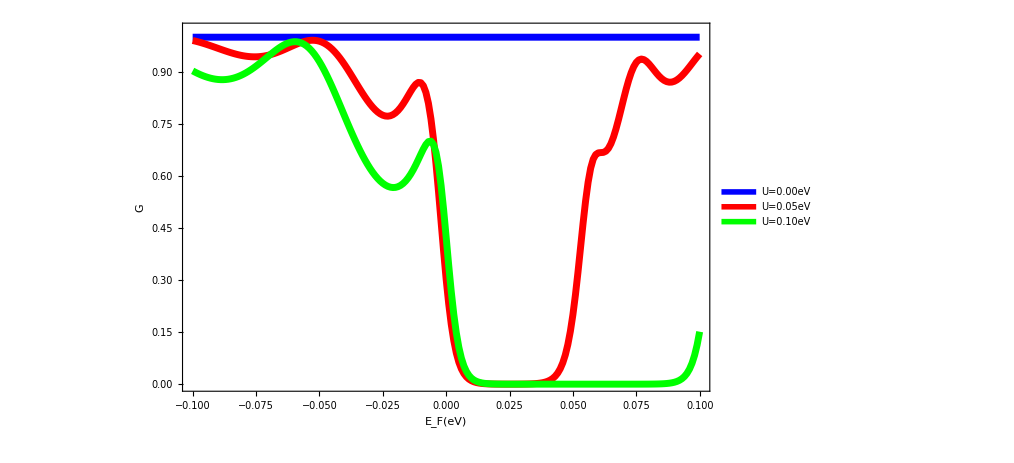

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,2}]];
data2=Import["TBG_tran22s.dat"][[All,{1,2}]];
data3=Import["TBG_tran32s.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{-0.1,0.1},{0,1.02}},ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["G",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

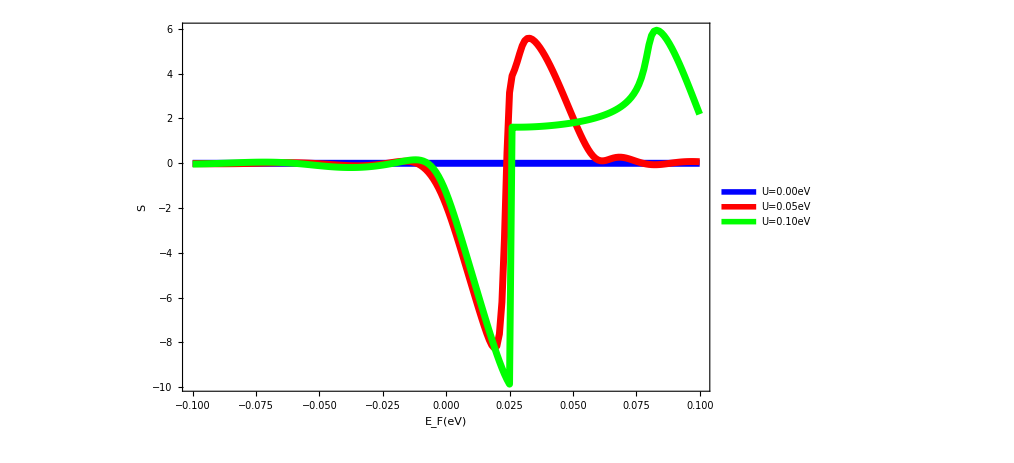

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,3}]];
data2=Import["TBG_tran22s.dat"][[All,{1,3}]];
data3=Import["TBG_tran32s.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["S",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

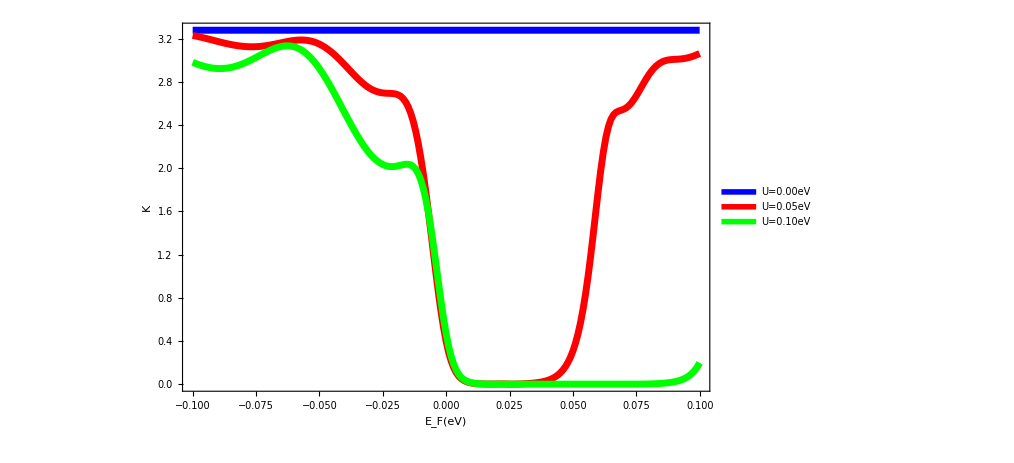

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,4}]];
data2=Import["TBG_tran22s.dat"][[All,{1,4}]];
data3=Import["TBG_tran32s.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["K",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

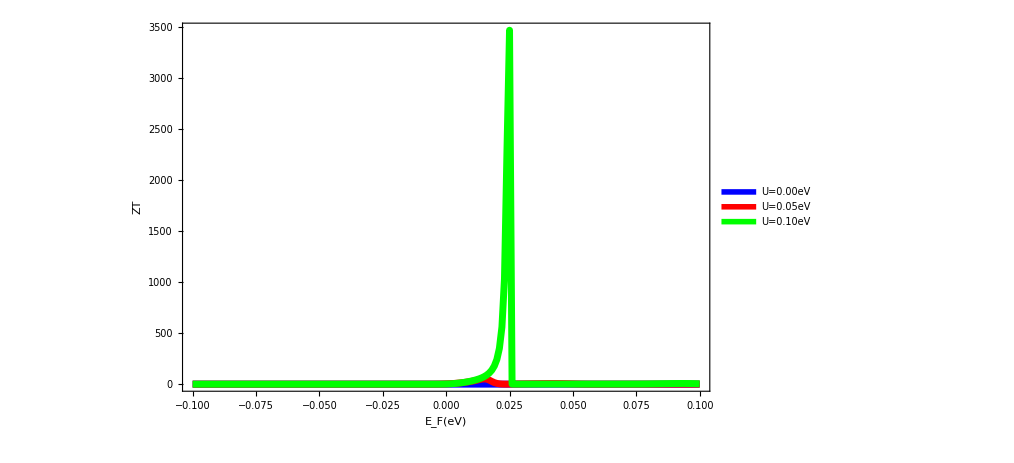

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,5}]];
data2=Import["TBG_tran22s.dat"][[All,{1,5}]];
data3=Import["TBG_tran32s.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["ZT",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

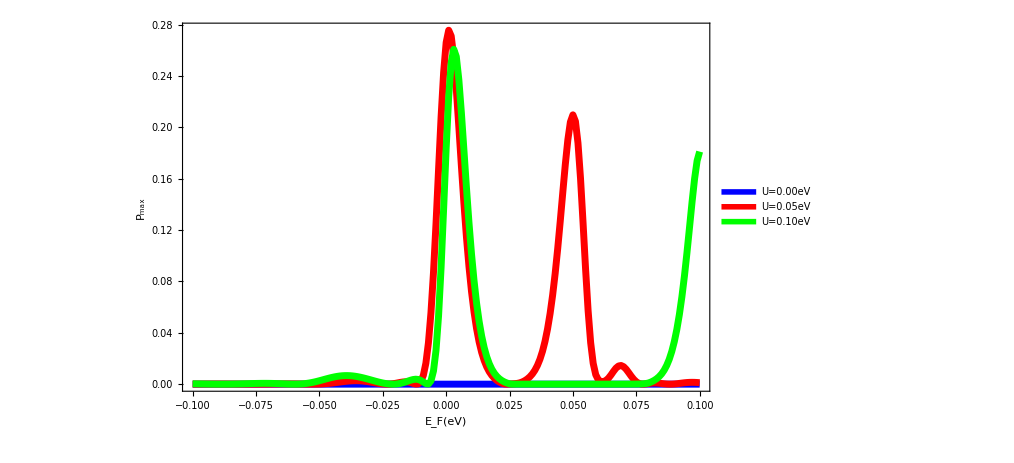

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,6}]];
data2=Import["TBG_tran22s.dat"][[All,{1,6}]];
data3=Import["TBG_tran32s.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["P_max",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

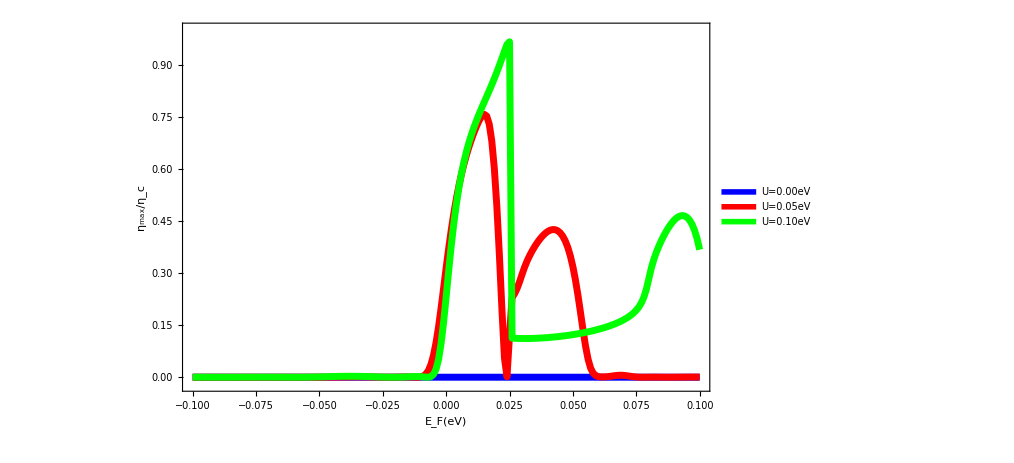

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,7}]];
data2=Import["TBG_tran22s.dat"][[All,{1,7}]];
data3=Import["TBG_tran32s.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->{{-0.1,0.1},{-0.02,1}},ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

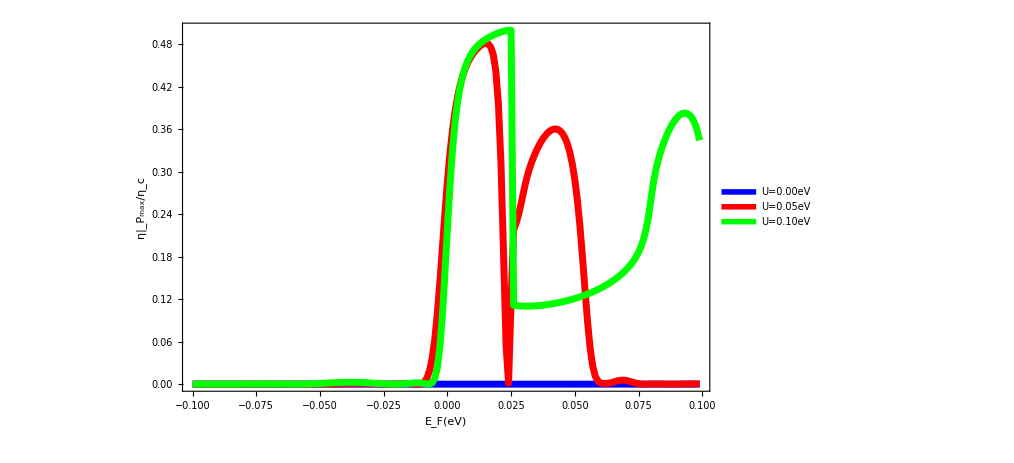

```mathematica
data1=Table[Flatten[{Import["TBG_tran12s.dat"][[x]][[1]],Import["TBG_tran12s.dat"][[x]][[5]]/(2Import["TBG_tran12s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data2=Table[Flatten[{Import["TBG_tran22s.dat"][[x]][[1]],Import["TBG_tran22s.dat"][[x]][[5]]/(2Import["TBG_tran22s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
data3=Table[Flatten[{Import["TBG_tran32s.dat"][[x]][[1]],Import["TBG_tran32s.dat"][[x]][[5]]/(2Import["TBG_tran32s.dat"][[x]][[5]]+4)}],{x,1,200,1}];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["η|_P_max/η_c",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

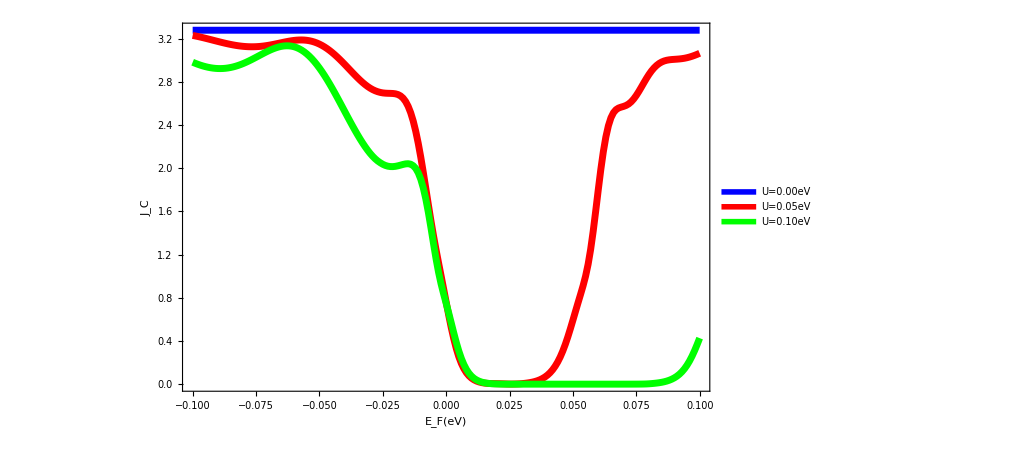

```mathematica
data1=Import["TBG_tran12s.dat"][[All,{1,8}]];
data2=Import["TBG_tran22s.dat"][[All,{1,8}]];
data3=Import["TBG_tran32s.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2,data3},Frame->True,PlotRange->All,ImageSize->750,PlotLegends->Placed[{"U=0.00eV","U=0.05eV","U=0.10eV"},{Left,Top}],FrameLabel->{Style["E_F(eV)",25,Black],Rotate[Style["J_C",25,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[5],Opacity[1],Blue],Directive[AbsoluteThickness[5],Opacity[1],Red],Directive[AbsoluteThickness[5],Opacity[1],Green],Directive[AbsoluteThickness[5],Opacity[1],Black],Directive[AbsoluteThickness[5],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[5],Opacity[1],Red, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Green, Dashed]},ImageSize->750,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

```mathematica
Clear["Global`*"]

a=1;

a1={Sqrt[3] a,0};
a2={Sqrt[3] a/2,3 a/2};

deltaA={0,0};
deltaB={Sqrt[3] a/2,a/2};

Nx=8;
Ny=5;

layer1A=Flatten[Table[n a1+m a2+deltaA,{n,0,Nx},{m,0,Ny}],1];

layer1B=Flatten[Table[n a1+m a2+deltaB,{n,0,Nx},{m,0,Ny}],1];

(*AB stacked second layer*)
shiftAB={Sqrt[3] a/2,a/2};

layer2A=layer1A+shiftAB+{0,0.3};
layer2B=layer1B+shiftAB+{0,0.3};

Graphics[{Blue,PointSize[0.015],Point[layer1A],Point[layer1B],Red,PointSize[0.015],Point[layer2A],Point[layer2B]},Axes->False,ImageSize->Large]
```

Thread::tdlen: Objects of unequal length in {{0,0},{(√3)/2,3/2},{√3,3},{(3 √3)/2,9/2},{2 √3,6},{(5 √3)/2,15/2},{√3,0},{(3 √3)/2,3/2},{2 √3,3},{(5 √3)/2,9/2},«44»}+{(√3)/2,1/2}+{0,0.3} cannot be combined.

Thread::tdlen: Objects of unequal length in {{(√3)/2,1/2},{√3,2},{(3 √3)/2,7/2},{2 √3,5},{(5 √3)/2,13/2},{3 √3,8},{(3 √3)/2,1/2},{2 √3,2},{(5 √3)/2,7/2},{3 √3,5},«44»}+{(√3)/2,1/2}+{0,0.3} cannot be combined.

-Graphics-

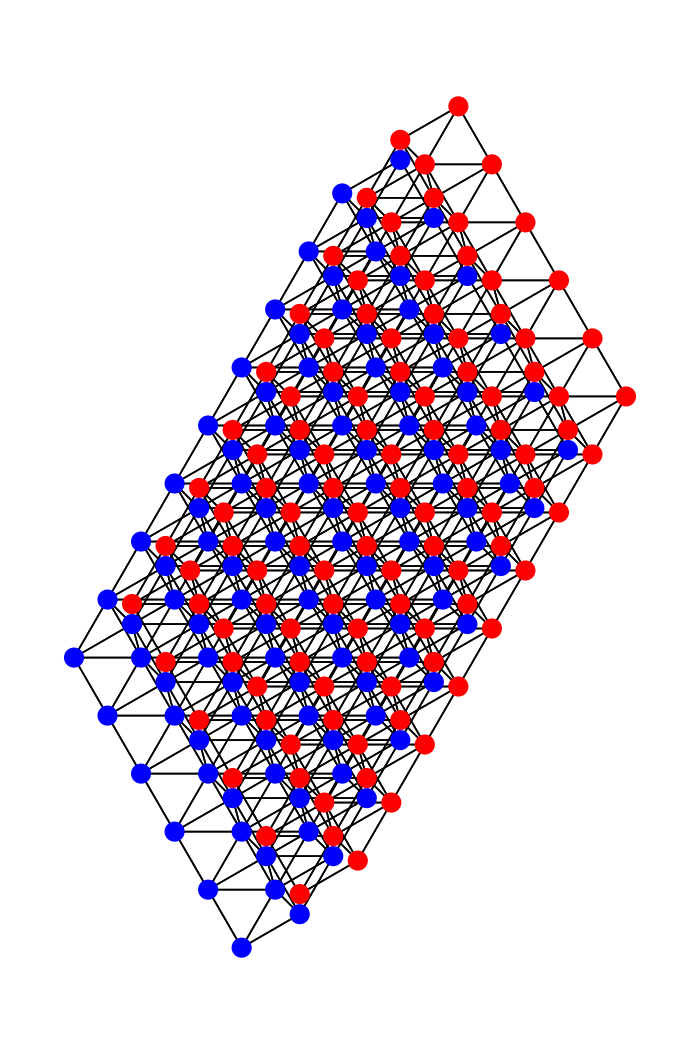

```mathematica
Clear["Global`*"]

(*Lattice constant*)
a=1;

(*Primitive vectors*)
a1={ a/2,Sqrt[3]a/2};
a2={-a/2,Sqrt[3]a/2};

(*Basis atoms*)
deltaA={0,0};
deltaB={Sqrt[3] a/2,a/2};

(*Number of unit cells*)
Nx=8;
Ny=5;

(*Bottom layer*)
layer1A=Flatten[Table[n a1+m a2+deltaA,{n,0,Nx},{m,0,Ny}],1];

layer1B=Flatten[Table[n a1+m a2+deltaB,{n,0,Nx},{m,0,Ny}],1];

(*AB stacking shift*)
shiftAB={Sqrt[3] a/2,a/2};

(*Small vertical offset for visual separation*)
zshift={0,0.3};

(*Top layer*)
layer2A=(#+shiftAB+zshift)&/@layer1A;
layer2B=(#+shiftAB+zshift)&/@layer1B;

(*All atoms*)
atoms1=Join[layer1A,layer1B];
atoms2=Join[layer2A,layer2B];

(*Nearest-neighbour bond length*)
bondLength=a;

(*Bonds bottom layer*)
bonds1=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,Line[{p,q}],Nothing],{p,atoms1},{q,atoms1}],1];

(*Bonds top layer*)
bonds2=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,Line[{p,q}],Nothing],{p,atoms2},{q,atoms2}],1];

Graphics[{Black,AbsoluteThickness[1.2],bonds1,Black,AbsoluteThickness[1.2],bonds2,Blue,Disk[#,0.15]&/@layer1A,Disk[#,0.15]&/@layer1B,Red,Disk[#,0.15]&/@layer2A,Disk[#,0.15]&/@layer2B},ImageSize->700,PlotRange->All]
```

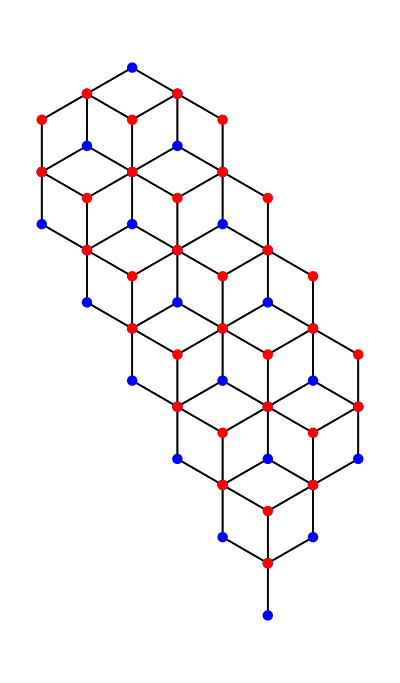

```mathematica
Clear["Global`*"]

a=1;

(*nearest-neighbour vectors*)
d1={0,a};
d2={Sqrt[3] a/2,-a/2};
d3={-Sqrt[3] a/2,-a/2};

(*primitive vectors*)
a1=d1-d2;
a2=d1-d3;

Nx=5;
Ny=2;

layer1A=Flatten[Table[n a1+m a2,{n,0,Nx},{m,0,Ny}],1];

layer1B=(#+d1)&/@layer1A;
(*AB stacking*)

shiftAB=d1;
zshift={0,0.0};

layer2A=(#+shiftAB+zshift)&/@layer1A;
layer2B=(#+shiftAB+zshift)&/@layer1B;

(*keep only rectangular region*)

xmin=Min[layer1A[[All,1]]];
xmax=Max[layer1A[[All,1]]];

ymin=Min[layer1A[[All,2]]];
ymax=Max[layer1A[[All,2]]];

rectQ[p_]:=xmin<=p[[1]]<=xmax&&ymin<=p[[2]]<=ymax;

layer1A=Select[layer1A,rectQ];
layer1B=Select[layer1B,rectQ];

layer2A=Select[layer2A,rectQ];
layer2B=Select[layer2B,rectQ];

atoms1=Join[layer1A,layer1B];
atoms2=Join[layer2A,layer2B];

bondLength=a;

bonds1=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,Line[{p,q}],Nothing],{p,atoms1},{q,atoms1}],1];

bonds2=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,Line[{p,q}],Nothing],{p,atoms2},{q,atoms2}],1];

Graphics[{Black,AbsoluteThickness[1.2],bonds1,bonds2,Blue,Disk[#,0.10]&/@layer1A,Disk[#,0.10]&/@layer2A,Red,Disk[#,0.10]&/@layer1B,Disk[#,0.10]&/@layer2B},ImageSize->400,PlotRange->All,Background->White]
```

```mathematica
Clear["Global`*"]

a=1;

(*nearest-neighbour vectors*)
d1={0,a};
d2={Sqrt[3] a/2,-a/2};
d3={-Sqrt[3] a/2,-a/2};

(*primitive vectors*)
a1=d1-d2;
a2=d1-d3;

Nx=8;
Ny=5;

(*bottom layer*)
layer1A=Flatten[Table[n a1+m a2,{n,0,Nx},{m,0,Ny}],1];

layer1B=(#+d1)&/@layer1A;

(*AB stacking*)
shiftAB=d1;

(*interlayer spacing for visualization*)
zsep=0.00;

layer2A=(#+shiftAB)&/@layer1A;
layer2B=(#+shiftAB)&/@layer1B;

atoms1=Join[layer1A,layer1B];
atoms2=Join[layer2A,layer2B];

bondLength=a;

(*intralayer bonds*)
bonds1=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,{Append[p,0],Append[q,0]},Nothing],{p,atoms1},{q,atoms1}],1];

bonds2=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,{Append[p,zsep],Append[q,zsep]},Nothing],{p,atoms2},{q,atoms2}],1];

A1=Graphics3D[{(*bonds*)Black,Tube[#,0.025]&/@bonds1,Tube[#,0.025]&/@bonds2,(*lower layer A*)RGBColor[0.1,0.2,0.9],Sphere[Append[#,0],0.12]&/@layer1A,(*lower layer B*)RGBColor[0.9,0.1,0.1],Sphere[Append[#,0],0.12]&/@layer1B,(*upper layer A*)RGBColor[0.3,0.5,1.0],Sphere[Append[#,zsep],0.12]&/@layer2A,(*upper layer B*)RGBColor[1.0,0.4,0.4],Sphere[Append[#,zsep],0.12]&/@layer2B},Boxed->False,Axes->False,Lighting->"Neutral",ViewPoint->{1,0.55,2},ImageSize->800,Background->White]
```

-Graphics3D-

```mathematica
ImageCrop[Rasterize[A1,ImageResolution->600],{Automatic,Automatic}]
```

-Graphics-

```mathematica
a=1;

(*nearest-neighbour vectors*)
d1={0,a};
d2={Sqrt[3] a/2,-a/2};
d3={-Sqrt[3] a/2,-a/2};

(*primitive vectors*)
a1=d1-d2;
a2=d1-d3;

Nx=10;
Ny=6;

(*Bottom layer*)
layer1A=Flatten[Table[n a1+m a2,{n,0,Nx},{m,0,Ny}],1];

layer1B=(#+d1)&/@layer1A;

(*Twist angle*)
theta=5 Degree;

rot=RotationTransform[theta];

(*Top layer*)
layer2A=rot/@layer1A;
layer2B=rot/@layer1B;

(*Interlayer spacing*)
zsep=0.35;

bondLength=a;

atoms1=Join[layer1A,layer1B];
atoms2=Join[layer2A,layer2B];

(*Bottom layer bonds*)
bonds1=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,{Append[p,0],Append[q,0]},Nothing],{p,atoms1},{q,atoms1}],1];

(*Top layer bonds*)
bonds2=Flatten[Table[If[0<Norm[p-q]<1.01 bondLength,{Append[p,zsep],Append[q,zsep]},Nothing],{p,atoms2},{q,atoms2}],1];

A2=Graphics3D[{(*bonds*)Black,Tube[#,0.025]&/@bonds1,Tube[#,0.025]&/@bonds2,(*lower layer A*)RGBColor[0.1,0.2,0.9],Sphere[Append[#,0],0.12]&/@layer1A,(*lower layer B*)RGBColor[0.9,0.1,0.1],Sphere[Append[#,0],0.12]&/@layer1B,(*upper layer A*)RGBColor[0.3,0.5,1.0],Sphere[Append[#,zsep],0.12]&/@layer2A,(*upper layer B*)RGBColor[1.0,0.4,0.4],Sphere[Append[#,zsep],0.12]&/@layer2B},Boxed->False,Axes->False,Lighting->"Neutral",ViewPoint->{1,0.55,2},ImageSize->800,Background->White]
```

-Graphics3D-

```mathematica
ImageCrop[Rasterize[A2,ImageResolution->600],{Automatic,Automatic}]
```

-Graphics-